### 2nd example support vector machine

In this example we build a classifier (using linear SVMs and the kernel trick explicitly) to classify data  whether it lies above or below a parabola or within an ellipse.

```mathematica
f2[x_]:=0.2 x^2
f3[x_]:=x[[1]]^2+0.5x[[2]]^2
```

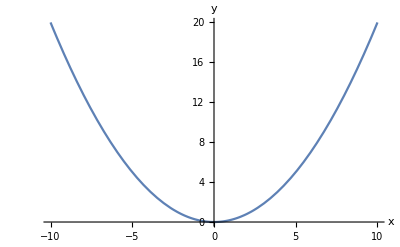

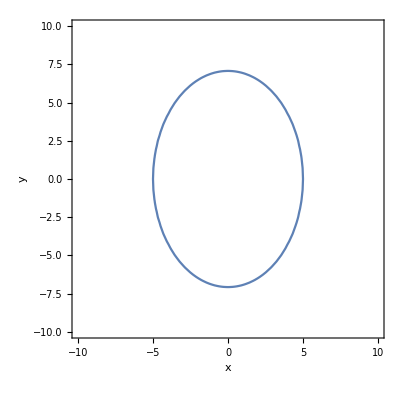

```mathematica
Plot[f2[x],{x,-10,10},AxesLabel->{"x","y"}]
ContourPlot[f3[{x,y}]==25,{x,-10,10},{y,-10,10},FrameLabel->{"x","y"}]
```

First of all we need to generate some random data points

```mathematica
alldata[n_]:=RandomReal[{-10,10},{n,2}]
```

We need to prepare a training data set:

```mathematica
ts2[datax_]:=Module[{data=datax},data2={};Do[If[(f2[data[[i,1]]]-data[[i,2]])≥0,data2=Append[data2,{data[[i]],1}],data2=Append[data2,{data[[i]],-1}]],{i,1,Length[data]}];data2]
ts3[datax_]:=Module[{data=datax},data2={};Do[If[(f3[data[[i]]])<=25,data2=Append[data2,{data[[i]],1}],data2=Append[data2,{data[[i]],-1}]],{i,1,Length[data]}];data2]
```

The following separates the two classes:

```mathematica
gb[datax_]:=Module[{data=datax},g={};b={};Do[If[data[[i,2]]==1,g=Append[g,data[[i,1]]],b=Append[b,data[[i,1]]]],{i,1,Length[data]}];{g,b}]
```

Let’s look at our data sets:

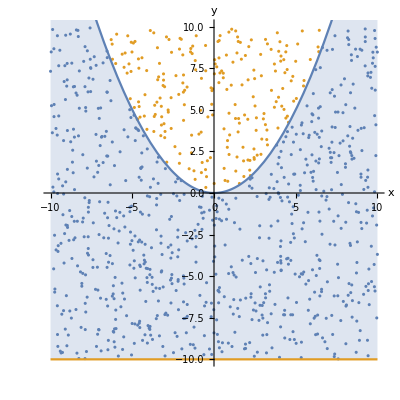

```mathematica
Show[ListPlot[gb[ts2[alldata[1000]]],PlotRange->{{-10,10},{-10,10}},AspectRatio->1,AxesLabel->{"x","y"}],Plot[{0.2 x^2,-10},{x,-10,10},Filling->{1->{2}}]]
```

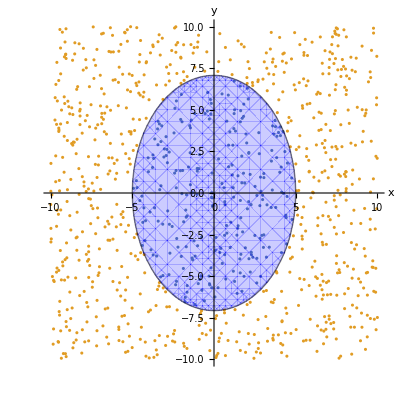

```mathematica
Show[ListPlot[gb[ts3[alldata[1000]]],PlotRange->{{-10,10},{-10,10}},AspectRatio->1,AxesLabel->{"x","y"}],ContourPlot[x^2+0.5y^2,{x,-10,10},{y,-10,10},Contours->{25},ContourShading->{Directive[Blue,Opacity[0.2]],None}]]
```

Let’s define a kernel map (for the ellipsoid):

```mathematica
kmb[x_]:={x[[1]]^2,x[[2]]^2};
```

Let’s look at the Kernel map with some data:

```mathematica
d2=alldata[10000];
d2a=gb[ts3[d2]][[1]];
d2b=gb[ts3[d2]][[2]];
```

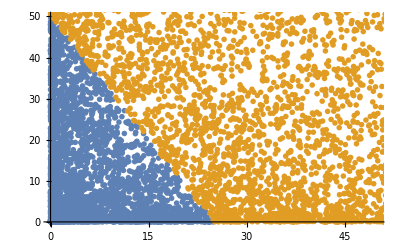

```mathematica
ListPlot[{Table[kmb[d2a[[i]]],{i,1,Length[d2a]}],Table[kmb[d2b[[i]]],{i,1,Length[d2b]}]},PlotRange->{{0,50},{0,50}},PlotStyle->PointSize[0.01]]
```

We can classify our data again using the same classifier as before (notebook01)...

Let’s look at the parabola:

```mathematica
kmc[x_]:={x[[1]]^2,x[[2]]};
```

```mathematica
d3=alldata[10000];
d3a=gb[ts2[d3]][[1]];
d3b=gb[ts2[d3]][[2]];
```

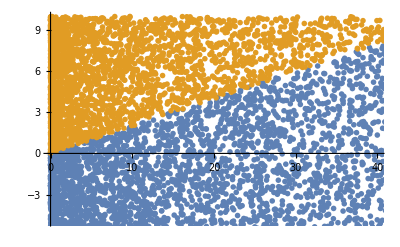

```mathematica
ListPlot[{Table[kmc[d3a[[i]]],{i,1,Length[d3a]}],Table[kmc[d3b[[i]]],{i,1,Length[d3b]}]},PlotRange->{{0,40},{-5,10}},PlotStyle->PointSize[0.01]]
```

Again we can classify data with our previous classifier (notebook01).